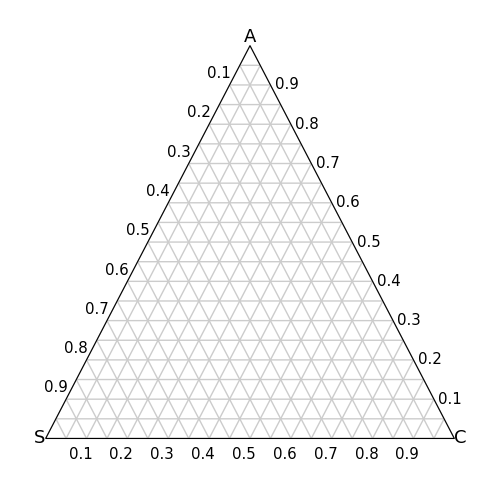

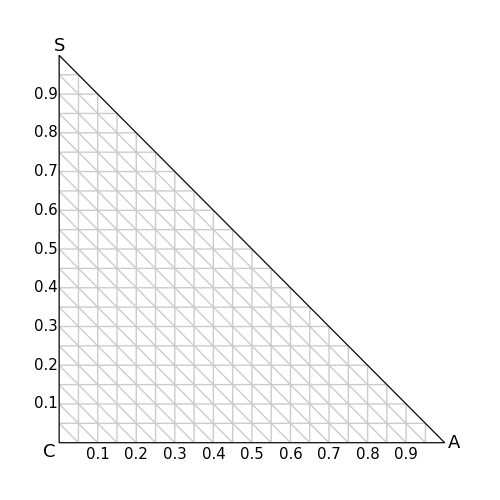

```mathematica
equilateral=Graphics[{
{GrayLevel[0.8],Thin,Table[{
Line[{{i/2,i*√3/2},{1-i/2,i*√3/2}}],
Line[{{i,0},{i/2,i*√3/2}}],
Line[{{1-i,0},{1-i/2,i*√3/2}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
Table[{Text[Style[j,15],{1.04-j/2,j*√3/2}],Rotate[Text[Style[1-j,15],{j/2-0.025,j*√3/2+0.025}],-55 Degree],Rotate[Text[Style[j,15],{j-0.015,-0.035}],55 Degree]},{j,0.1,0.9,0.1}],
Text[Style["A",18],{0.5,√3/2},{0,-1}],Text[Style["S  ",18],{0,0},{1,0}],Text[Style["  C",18],{1,0},{-1,0}]
},AspectRatio->1,ImageSize->500]

right=Graphics[{
{Thin,GrayLevel[0.8],
Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],
(*Text[Style["solvent  mass  fraction ⟶",17],{-0.1,0.5},{0,0},{0,1}],
Text[Style["solute mass fraction ⟶",17],{0.5,-0.1}],*)
Text[Style["S",18],{0,1.025}],Text[Style["A",18],{1.025,0}],Text[Style["C",18],{-0.025,-0.025}]
},AspectRatio->1,ImageSize->500]
```